```mathematica
ChromaticPolynomial[CycleGraph[n],x]
```

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[CycleGraph[n], x].

```mathematica
Table[ChromaticPolynomial[CycleGraph[n],x],{n,0,10}]
```

CycleGraph::intpm: Positive machine-sized integer expected at position 1 in CycleGraph[0].

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[CycleGraph[0], x].

{ChromaticPolynomial[CycleGraph[0],x],0,-x+x^2,2 x-3 x^2+x^3,-3 x+6 x^2-4 x^3+x^4,4 x-10 x^2+10 x^3-5 x^4+x^5,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,8 x-36 x^2+84 x^3-126 x^4+126 x^5-84 x^6+36 x^7-9 x^8+x^9,-9 x+45 x^2-120 x^3+210 x^4-252 x^5+210 x^6-120 x^7+45 x^8-10 x^9+x^10}

```mathematica
With[
{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3, X5=-3 x+6 x^2-4 x^3+x^4,e=1},
Solve[Element[a|b|c|d|e,Reals]&& a X1 + b X2 + c X3 +d X4 + e X5==ChromaticPolynomial[ReadGrof[1],x],{a,b,c,d,e}]
]
```

Solve::ivar: 1 is not a valid variable.

Solve[(a|b|c|d)∈Reals&&a-3 x+b x+6 x^2-4 x^3+x^4+c (-x+x^2)+d (2 x-3 x^2+x^3)==-6 x+11 x^2-6 x^3+x^4,{a,b,c,d,1}]

```mathematica
ChromaticPolynomial[ReadGrof[1],x]
```

-6 x+11 x^2-6 x^3+x^4

```mathematica
With[
{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3, X5=-3 x+6 x^2-4 x^3+x^4,e=1,d=-2,c=-1,b=-1},
Factor[a X1 + b X2 + c X3 +d X4 + e X5 -(-6 x+11 x^2-6 x^3+x^4)]
]
```

a-x

```mathematica
ChromaticPolynomial[ReadGrof[2],x]
```

18 x-39 x^2+29 x^3-9 x^4+x^5

```mathematica
With[
{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3, X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,f=1,e=-4,d=3,c=4,b=-1},
Factor[a X1 + b X2 + c X3 +d X4 + e X5 +f X6-(18 x-39 x^2+29 x^3-9 x^4+x^5)]
]
```

a-x

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,g=1,f=-6,e=11,d=-2,c=-12,b=-1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7-(-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)]]
```

a-x

```mathematica
ChromaticPolynomial[ReadGrof[3],x]
```

-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,h=0,g=1,f=-6,e=13,d=-5,c=-14,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8-(-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6)]]
```

1-x

```mathematica
ChromaticPolynomial[ReadGrof[4],x]
```

-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6

```mathematica
ChromaticPolynomial[ReadGrof[5],x]
```

162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,h=1,g=-8,f=23,e=-24,d=-8,c=32,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8-(162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7)]]
```

1-x

```mathematica
ChromaticPolynomial[ReadGrof[7],x]
```

210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,h=1,g=-8,f=26,e=-35,d=-1,c=43,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8-(210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7)]]
```

1-x

```mathematica
ChromaticPolynomial[ReadGrof[8],x]
```

162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,h=1,g=-8,f=23,e=-24,d=-8,c=32,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8-(162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7)]]
```

1-x

```mathematica
ChromaticPolynomial[ReadGrof[9],x]
```

162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,h=1,g=-8,f=23,e=-24,d=-8,c=32,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8-(162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7)]]
```

```mathematica
IsomorphicGraphQ[ReadGrof[8],ReadGrof[9]]
```

False

```mathematica
ChromaticPolynomial[ReadGrof[10],x]
```

-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,X9=-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,i=1,h=-10,g=39,f=-70,e=40,d=48,c=-80,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8+i X9-(-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8)]]
```

1-x

```mathematica
ChromaticPolynomial[ReadGrof[11],x]
```

-630 x+1905 x^2-2347 x^3+1554 x^4-605 x^5+140 x^6-18 x^7+x^8

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,X9=-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,
i=1,h=-10,g=42,f=-87,e=69,d=45,c=-112,b=1,a=-1},
Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8+i X9-(-630 x+1905 x^2-2347 x^3+1554 x^4-605 x^5+140 x^6-18 x^7+x^8)]]
```

-1+x

```mathematica
ChromaticPolynomial[ReadGrof[12],x]
```

-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,X9=-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,
i=1,h=-10},
Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8+i X9-(-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8)]]
```

a+419 x+b x-c x+2 d x-3 e x+4 f x-5 g x-1301 x^2+c x^2-3 d x^2+6 e x^2-10 f x^2+15 g x^2+1592 x^3+d x^3-4 e x^3+10 f x^3-20 g x^3-975 x^4+e x^4-5 f x^4+15 g x^4+304 x^5+f x^5-6 g x^5-39 x^6+g x^6

```mathematica
Coefficient[-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8]
```

0

```mathematica
BaseCoeff[x]
```

{x}

```mathematica
CyclePoly[1]:=x
CyclePoly[n_]:=CyclePoly[n]=ChromaticPolynomial[CycleGraph[n],x]
```

```mathematica
CycleBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥2,pos--,
current = CyclePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
AppendTo[result,poly];
result
]
```

```mathematica
ChromaticPolynomial[JacobsThalGraph[2],x]
```

-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6

```mathematica
ChromaticPolynomial[JacobsThalGraph[3],x]
```

210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7

```mathematica
EulerBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥4,pos--,
current =ChromaticPolynomial[ JacobsThalGraph[pos-4],x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
AppendTo[result,poly];
result
]
```

```mathematica
TableForm[Table[EulerBaseCoeff[ChromaticPolynomial[DiamondGraph[k],x]],{k,0,10}]]
```

x^2 |  |  |  |  |  |  |  | 
x-2 x^2+x^3 |  |  |  |  |  |  |  | 
-4 x+8 x^2-5 x^3+x^4 |  |  |  |  |  |  |  | 
1 | (-2+x)^2 (-1+x) x |  |  |  |  |  |  | 
1 | 1 | 0 |  |  |  |  |  | 
1 | 1 | 0 | 0 |  |  |  |  | 
1 | 1 | 0 | 0 | 0 |  |  |  | 
1 | 1 | 0 | 0 | 0 | 0 |  |  | 
1 | 1 | 0 | 0 | 0 | 0 | 0 |  | 
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
TableForm[Table[EulerBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]],{k,10000,10150}]]
```

1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -4 | -28 | -33 | 144 | 464 | 49 | -1338 | 808/7 | -1/7 (-2+x) (-1+x) x (-13389+808 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -9 | -28 | 0 | 218 | 424 | -340 | -1606 | 263/7 | -1/7 (-2+x) (-1+x) x (-5784+263 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -6 | -27 | -21 | 167 | 444 | -87 | -1413 | 607/7 | -1/7 (-2+x) (-1+x) x (-10555+607 x (3+x))
1 | 0 | -5 | -29 | -29 | 164 | 479 | -20 | -1450 | 746/7 | -1/7 (-2+x) (-1+x) x (-12623+746 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))
1 | 0 | -7 | -27 | -14 | 182 | 434 | -168 | -1464 | 491/7 | -1/7 (-2+x) (-1+x) x (-8929+491 x (3+x))

```mathematica
TableForm[Table[BaseCoeff[ChromaticPolynomial[DiamondGraph[k],x]],{k,2,10}]]
```

1 | -1 | -1 | 0 |  |  |  |  |  |  |  | 
1 | -3 | 2 | 3 | 0 |  |  |  |  |  |  | 
1 | -5 | 9 | -2 | -10 | 0 |  |  |  |  |  | 
1 | -7 | 20 | -22 | -6 | 29 | 0 |  |  |  |  | 
1 | -9 | 35 | -65 | 40 | 43 | -76 | 0 |  |  |  | 
1 | -11 | 54 | -139 | 175 | -37 | -167 | 187 | 0 |  |  | 
1 | -13 | 77 | -252 | 462 | -392 | -98 | 530 | -442 | 0 |  | 
1 | -15 | 104 | -412 | 980 | -1330 | 686 | 740 | -1516 | 1017 | 0 | 
1 | -17 | 135 | -627 | 1824 | -3318 | 3360 | -618 | -3024 | 4069 | -2296 | 0

```mathematica
FindGeneratingFunction[{3,9,27,85,269,771,2267,6801,19289},x]
```

FindGeneratingFunction[{3,9,27,85,269,771,2267,6801,19289},x]

```mathematica
VertexCount[JacobsThalGraph[4]]
```

8

```mathematica
BaseCoeff[ChromaticPolynomial[JacobsThalGraph[4],x]]
```

{1,-10,43,-91,75,44,-119,0}

```mathematica
TableForm[
Table[With[
{g=BaseCoeff[ChromaticPolynomial[JacobsThalGraph[k],x]]},
{g,Total[Abs[g]],Total[g],k,VertexCount[ReadGrof[k]]}],{k,1,10}],
TableDepth->2, TableAlignments->Right
]
```

{1,-4,3,4,0} | 12 | 4 | 1 | 4
{1,-6,13,-5,-14,0} | 39 | -11 | 2 | 5
{1,-8,26,-35,-1,43,0} | 114 | 26 | 3 | 6
{1,-10,43,-91,75,44,-119,0} | 383 | -57 | 4 | 6
{1,-12,64,-182,266,-112,-211,306,0} | 1154 | 120 | 5 | 7
{1,-14,89,-316,644,-658,14,741,-748,0} | 3225 | -247 | 6 | 7
{1,-16,118,-501,1296,-1974,1344,726,-2257,1765,0} | 9998 | 502 | 7 | 7
{1,-18,151,-745,2325,-4614,5334,-1962,-3750,6326,-4061,0} | 29287 | -1013 | 8 | 7
{1,-20,188,-1056,3850,-9339,14652,-12672,132,13915,-16787,9172,0} | 81784 | 2036 | 9 | 7
{1,-22,229,-1442,6006,-17149,33495,-42108,25476,13783,-44781,42855,-20426,0} | 247773 | -4083 | 10 | 8

```mathematica
Exponent[CyclePoly[2],x]
```

2

```mathematica
CyclePoly[1]
```

x

```mathematica
With[{X1=1,X2=x,X3=-x+x^2,X4=2 x-3 x^2+x^3,X5=-3 x+6 x^2-4 x^3+x^4,X6=4 x-10 x^2+10 x^3-5 x^4+x^5,X7=-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6,X8=6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7,h=0,g=1,f=-6,e=13,d=-5,c=-14,b=-1,a=1},Factor[a X1+b X2+c X3+d X4+e X5+f X6+g X7+h X8-(-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6)]]
```

```mathematica
Monitor[
Table[With[
{g=BaseCoeff[ChromaticPolynomial[ReadGrof[k],x]]},
{VertexCount[ReadGrof[k]],Total[g]}],{k,1,2000}],k]
```

{{4,-2},{5,4},{6,-8},{6,-11},{7,16},{7,22},{7,26},{7,16},{7,16},{8,-32},{8,-52},{8,-32},{8,-32},{8,-44},{8,-44},{8,-32},{8,-32},{8,-66},{8,-44},{8,-44},{8,-57},1958,{12,-832},{12,-832},{12,-832},{12,-832},{12,-832},{12,-832},{12,-832},{12,-832},{12,-832},{12,-832},{12,-1352},{12,-1296},{12,-1888},{12,-832},{12,-1448},{12,-1720},{12,-832},{12,-1056},{12,-1456},{12,-1456},{12,-1056}}
 |  |  |  |

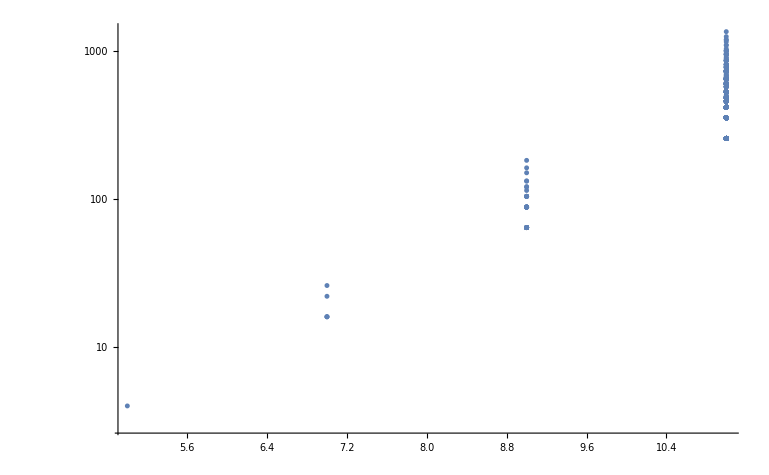

```mathematica
ListLogPlot[%,PlotRange->All]
```

```mathematica
Table[{i,j},{i,1,4},{j,1,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}}}

```mathematica
All=Select[Flatten[Table[{i,j},{i,1,4},{j,1,4}],1],#[[1]]<#[[2]]&]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
Sort[Block[
{nodes=5, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{BaseCoeff[ChromaticPolynomial[g,x]],ConnectedGraphQ[g]}
],{current,edgeSets}]
]]
```

{{{1,-5,5,5,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},{{1,-4,3,4,0},True},1005,{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False},{{1,4,6,4,0},False}}
 |  |  |  |

```mathematica
First[Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,6},{j,1,6}],1],#[[1]]<#[[2]]&]],#≠{}&]]
```

{{1,2}}

```mathematica
IsomorphicGraphQ
```


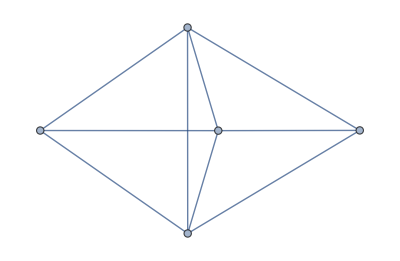
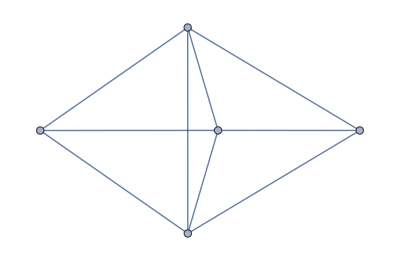
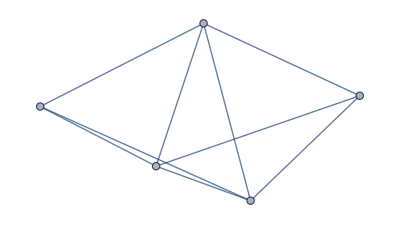
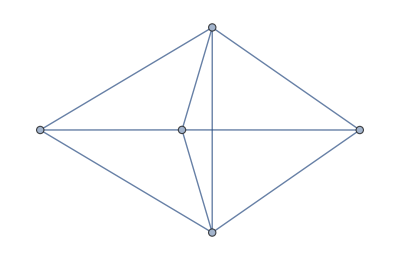
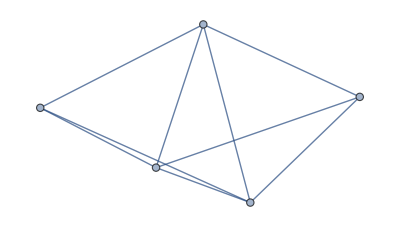
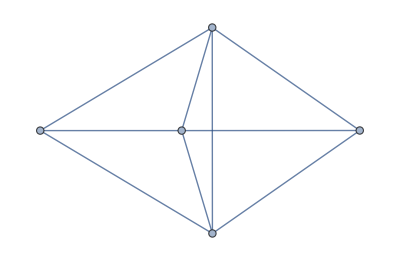
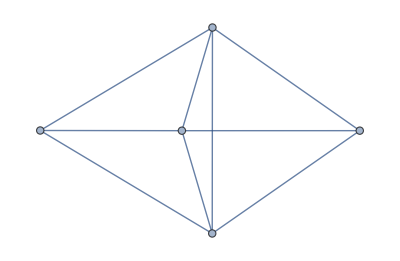
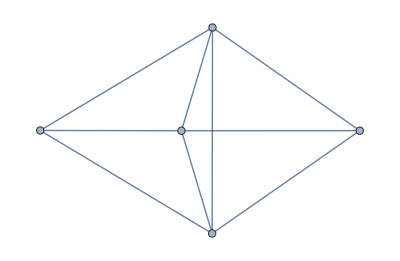
{{{1,-5,5,5,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-4,3,4,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,1,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-3,2,3,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,-1,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},{{1,-2,0,2,0},-Graphics-},813,{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,2,1,0,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,3,3,1,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-},{{1,4,6,4,0},-Graphics-}}
 |  |  |  |

```mathematica
Sort[Block[
{nodes=5, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{BaseCoeff[ChromaticPolynomial[g,x]],Graph[g,ImageSize->Tiny]}
],{current,edgeSets}]
]]
```

```mathematica
bonjour
```

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=5, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Map[#[[2]]&,
Select[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{ConnectedGraphQ[g], BaseCoeff[ChromaticPolynomial[g,x]]}
],{current,edgeSets}]
,#[[1]]&
]
]
]
]
],
TableDepth->1
]
```

{1,-5,5,5,0}
{1,-4,3,4,0}
{1,-3,1,3,0}
{1,-3,2,3,0}
{1,-2,-1,2,0}
{1,-2,0,2,0}
{1,-2,1,2,0}
{1,-1,-1,1,0}
{1,-1,0,1,0}
{1,-1,1,2,0}
{1,0,-1,0,0}
{1,0,0,0,0}
{1,0,0,1,0}
{1,1,0,0,0}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=6, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Map[#[[2]]&,
Select[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{ConnectedGraphQ[g], BaseCoeff[ChromaticPolynomial[g,x]]}
],{current,edgeSets}]
,#[[1]]&
]
]
]
]
],
TableDepth->1
]
```

0
1

```mathematica
Block[
{nodes=6, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Map[With[{k=#[[2]]},k[[1]]+k[[3]]+k[[5]]]&,
Select[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{ConnectedGraphQ[g], BaseCoeff[ChromaticPolynomial[g,x]]}
],{current,edgeSets}]
,#[[1]]&
]
]
]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,26505,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Block[
{nodes=5, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Map[With[{k=#[[2]]},k[[2]]+k[[4]]]&,
Select[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{ConnectedGraphQ[g], BaseCoeff[ChromaticPolynomial[g,x]]}
],{current,edgeSets}]
,#[[1]]&
]
]
]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=2, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
Abs[BaseCoeff[ChromaticPolynomial[g,x]]]
],{current,edgeSets}]
]
]
],
TableDepth->1
]
```

{1,0}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=3, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
Abs[BaseCoeff[ChromaticPolynomial[g,x]]]
],{current,edgeSets}]
]
]
],
TableDepth->1
]
```

{1,0,0}
{1,1,0}
{1,2,0}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=4, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
Abs[BaseCoeff[ChromaticPolynomial[g,x]]]
],{current,edgeSets}]
]
]
],
TableDepth->1
]
```

{1,0,0,0}
{1,0,1,0}
{1,1,0,0}
{1,1,1,0}
{1,2,1,0}
{1,3,3,0}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=5, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current]]},
{PlanarGraphQ[g], Abs[BaseCoeff[ChromaticPolynomial[g,x]]]}
],{current,edgeSets}]
]
]
],
TableDepth->1
]
```

{False,{1,5,5,5,0}}
{True,{1,0,0,0,0}}
{True,{1,0,0,1,0}}
{True,{1,0,1,0,0}}
{True,{1,0,2,0,0}}
{True,{1,1,0,0,0}}
{True,{1,1,0,1,0}}
{True,{1,1,1,1,0}}
{True,{1,1,1,2,0}}
{True,{1,1,3,1,0}}
{True,{1,2,0,2,0}}
{True,{1,2,1,0,0}}
{True,{1,2,1,2,0}}
{True,{1,3,1,3,0}}
{True,{1,3,2,3,0}}
{True,{1,3,3,1,0}}
{True,{1,4,3,4,0}}
{True,{1,4,6,4,0}}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=6, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Monitor[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current2]]},
{ Abs[BaseCoeff[ChromaticPolynomial[g,x]]],PlanarGraphQ[g]}
],{current2,edgeSets}],
current2]
]
]
],
TableDepth->1
]
```

{{1,0,0,0,0,0},True}
{{1,0,0,0,1,0},True}
{{1,0,0,1,0,0},True}
{{1,0,0,3,1,0},True}
{{1,0,1,0,0,0},True}
{{1,0,1,1,0,0},True}
{{1,0,2,0,1,0},True}
{{1,0,4,2,3,0},True}
{{1,1,0,0,0,0},True}
{{1,1,0,0,1,0},True}
{{1,1,0,1,1,0},True}
{{1,1,1,0,2,0},True}
{{1,1,1,1,0,0},True}
{{1,1,1,1,1,0},True}
{{1,1,1,2,1,0},True}
{{1,1,1,3,0,0},True}
{{1,1,2,2,1,0},True}
{{1,1,3,1,2,0},True}
{{1,2,0,2,1,0},True}
{{1,2,1,0,0,0},True}
{{1,2,1,0,2,0},True}
{{1,2,1,1,2,0},True}
{{1,2,1,2,0,0},True}
{{1,2,1,2,2,0},True}
{{1,2,1,5,0,0},True}
{{1,2,2,0,3,0},True}
{{1,2,2,1,3,0},True}
{{1,2,2,4,1,0},True}
{{1,2,3,1,3,0},True}
{{1,2,3,2,3,0},True}
{{1,3,1,3,2,0},True}
{{1,3,1,7,0,0},True}
{{1,3,2,1,3,0},True}
{{1,3,2,2,3,0},True}
{{1,3,2,3,3,0},True}
{{1,3,3,0,4,0},True}
{{1,3,3,1,0,0},True}
{{1,3,3,1,4,0},True}
{{1,3,4,0,5,0},True}
{{1,3,4,1,5,0},True}
{{1,3,6,1,6,0},False}
{{1,4,0,10,1,0},False}
{{1,4,3,4,4,0},True}
{{1,4,4,2,5,0},True}
{{1,4,5,0,6,0},True}
{{1,4,5,1,6,0},True}
{{1,4,6,0,7,0},True}
{{1,4,6,1,7,0},True}
{{1,4,6,4,1,0},True}
{{1,4,7,2,8,0},False}
{{1,5,5,5,6,0},False}
{{1,5,7,1,8,0},True}
{{1,5,8,1,9,0},False}
{{1,5,8,1,9,0},True}
{{1,5,9,2,10,0},False}
{{1,5,9,2,10,0},True}
{{1,5,9,3,10,0},False}
{{1,5,10,10,5,0},True}
{{1,6,10,0,11,0},False}
{{1,6,11,2,12,0},False}
{{1,6,11,2,12,0},True}
{{1,6,12,4,13,0},False}
{{1,6,13,5,14,0},True}
{{1,7,15,5,16,0},False}
{{1,7,16,7,17,0},False}
{{1,8,20,10,21,0},False}
{{1,9,25,15,26,0},False}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=7, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Monitor[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current2]]},
{ BaseCoeff[ChromaticPolynomial[g,x]],PlanarGraphQ[g]}
],{current2,edgeSets}],
current2]
]
]
],
TableDepth->1
]
```

{{1,0,0,0,0,0,0},True}
{{1,0,0,0,0,1,0},True}
{{1,0,0,0,1,0,0},True}
{{1,0,0,1,0,0,0},True}
{{1,0,0,1,2,1,0},True}
{{1,0,0,2,0,0,0},True}
{{1,0,0,3,1,1,0},True}
{{1,0,1,0,0,0,0},True}
{{1,0,1,0,1,0,0},True}
{{1,0,1,1,0,1,0},True}
{{1,0,2,0,1,0,0},True}
{{1,0,2,2,3,2,0},True}
{{1,0,3,0,3,0,0},True}
{{1,0,4,2,3,2,0},True}
{{1,1,0,0,0,0,0},True}
{{1,1,0,0,0,1,0},True}
{{1,1,0,0,1,1,0},True}
{{1,1,0,1,1,0,0},True}
{{1,1,0,2,3,1,0},True}
{{1,1,0,3,2,2,0},True}
{{1,1,0,3,4,0,0},True}
{{1,1,1,0,0,2,0},True}
{{1,1,1,0,1,1,0},True}
{{1,1,1,0,2,1,0},True}
{{1,1,1,1,0,0,0},True}
{{1,1,1,1,1,1,0},True}
{{1,1,1,1,1,2,0},True}
{{1,1,1,1,2,0,0},True}
{{1,1,1,2,1,0,0},True}
{{1,1,1,2,1,1,0},True}
{{1,1,1,3,0,2,0},True}
{{1,1,1,4,2,1,0},True}
{{1,1,1,5,1,2,0},True}
{{1,1,2,2,1,1,0},True}
{{1,1,3,1,2,0,0},True}
{{1,1,3,4,5,3,0},True}
{{1,1,4,2,5,1,0},True}
{{1,1,4,6,1,5,0},True}
{{1,2,0,2,1,0,0},True}
{{1,2,0,3,4,1,0},True}
{{1,2,0,4,3,2,0},True}
{{1,2,1,0,0,0,0},True}
{{1,2,1,0,0,2,0},True}
{{1,2,1,0,1,2,0},True}
{{1,2,1,0,2,2,0},True}
{{1,2,1,1,2,1,0},True}
{{1,2,1,2,0,0,0},True}
{{1,2,1,2,2,0,0},True}
{{1,2,1,3,2,1,0},True}
{{1,2,1,3,6,1,0},True}
{{1,2,1,4,1,2,0},True}
{{1,2,1,4,5,2,0},True}
{{1,2,1,5,0,3,0},True}
{{1,2,1,5,4,3,0},True}
{{1,2,2,0,2,2,0},True}
{{1,2,2,0,3,2,0},True}
{{1,2,2,1,1,3,0},True}
{{1,2,2,1,2,3,0},True}
{{1,2,2,1,3,1,0},True}
{{1,2,2,2,1,4,0},True}
{{1,2,2,4,1,2,0},True}
{{1,2,3,0,2,3,0},True}
{{1,2,3,1,1,4,0},True}
{{1,2,3,1,2,3,0},True}
{{1,2,3,1,3,2,0},True}
{{1,2,3,1,3,3,0},True}
{{1,2,3,2,2,4,0},True}
{{1,2,3,2,3,1,0},True}
{{1,2,3,2,3,4,0},True}
{{1,2,3,5,7,1,0},False}
{{1,2,4,6,7,4,0},True}
{{1,3,0,6,3,3,0},True}
{{1,3,1,3,2,0,0},True}
{{1,3,1,5,6,2,0},True}
{{1,3,1,6,5,3,0},True}
{{1,3,1,7,0,4,0},True}
{{1,3,2,0,1,3,0},True}
{{1,3,2,1,3,2,0},True}
{{1,3,2,2,3,1,0},True}
{{1,3,2,3,3,0,0},True}
{{1,3,2,5,8,2,0},True}
{{1,3,2,6,7,3,0},True}
{{1,3,3,0,3,3,0},True}
{{1,3,3,0,4,3,0},True}
{{1,3,3,1,0,0,0},True}
{{1,3,3,1,1,4,0},True}
{{1,3,3,1,2,4,0},True}
{{1,3,3,1,4,2,0},True}
{{1,3,3,2,3,3,0},True}
{{1,3,3,5,10,2,0},False}
{{1,3,4,0,5,3,0},True}
{{1,3,4,1,3,4,0},True}
{{1,3,4,1,4,4,0},True}
{{1,3,4,1,5,2,0},True}
{{1,3,4,1,5,4,0},True}
{{1,3,4,2,2,5,0},True}
{{1,3,4,2,3,5,0},True}
{{1,3,4,3,1,6,0},True}
{{1,3,4,3,2,6,0},True}
{{1,3,4,3,3,6,0},True}
{{1,3,4,10,9,7,0},False}
{{1,3,5,1,5,4,0},True}
{{1,3,5,2,4,5,0},True}
{{1,3,5,3,3,6,0},True}
{{1,3,5,3,4,6,0},True}
{{1,3,5,4,2,7,0},True}
{{1,3,5,4,3,7,0},True}
{{1,3,6,0,5,4,0},True}
{{1,3,6,1,6,5,0},False}
{{1,3,6,2,4,6,0},True}
{{1,3,6,3,3,7,0},True}
{{1,3,6,5,2,8,0},False}
{{1,4,0,10,1,6,0},False}
{{1,4,2,8,7,4,0},True}
{{1,4,3,4,4,0,0},True}
{{1,4,3,7,10,3,0},False}
{{1,4,3,7,10,3,0},True}
{{1,4,4,2,5,2,0},True}
{{1,4,4,6,13,2,0},False}
{{1,4,4,7,12,3,0},False}
{{1,4,4,7,12,3,0},True}
{{1,4,5,0,5,4,0},True}
{{1,4,5,0,6,4,0},True}
{{1,4,5,1,4,5,0},True}
{{1,4,5,1,6,3,0},True}
{{1,4,5,2,2,6,0},True}
{{1,4,6,0,7,4,0},True}
{{1,4,6,1,7,5,0},True}
{{1,4,6,2,4,6,0},True}
{{1,4,6,2,5,6,0},True}
{{1,4,6,3,3,7,0},True}
{{1,4,6,3,4,7,0},True}
{{1,4,6,3,5,7,0},True}
{{1,4,6,4,1,0,0},True}
{{1,4,6,4,2,8,0},True}
{{1,4,6,4,3,8,0},True}
{{1,4,7,2,8,6,0},False}
{{1,4,7,3,6,7,0},True}
{{1,4,7,4,4,8,0},True}
{{1,4,7,4,5,8,0},True}
{{1,4,7,5,3,9,0},True}
{{1,4,7,5,4,9,0},True}
{{1,4,7,5,5,9,0},True}
{{1,4,7,6,2,10,0},False}
{{1,4,7,6,2,10,0},True}
{{1,4,7,6,3,10,0},True}
{{1,4,8,3,7,7,0},True}
{{1,4,8,5,5,9,0},True}
{{1,4,8,5,6,9,0},True}
{{1,4,8,6,4,10,0},True}
{{1,4,8,6,5,10,0},True}
{{1,4,8,7,3,11,0},False}
{{1,4,8,7,4,11,0},True}
{{1,4,8,8,2,12,0},True}
{{1,4,9,7,5,11,0},False}
{{1,4,9,9,2,13,0},False}
{{1,4,10,8,4,13,0},False}
{{1,5,4,10,11,5,0},False}
{{1,5,5,5,6,0,0},False}
{{1,5,5,9,14,4,0},False}
{{1,5,5,9,14,4,0},True}
{{1,5,6,8,17,3,0},False}
{{1,5,7,1,8,4,0},True}
{{1,5,7,8,19,3,0},True}
{{1,5,8,1,9,6,0},False}
{{1,5,8,1,9,6,0},True}
{{1,5,8,2,7,7,0},True}
{{1,5,8,3,5,8,0},True}
{{1,5,8,4,3,9,0},False}
{{1,5,9,2,10,7,0},False}
{{1,5,9,2,10,7,0},True}
{{1,5,9,3,10,8,0},False}
{{1,5,9,4,7,9,0},True}
{{1,5,9,5,5,10,0},True}
{{1,5,9,5,6,10,0},True}
{{1,5,9,6,4,11,0},True}
{{1,5,9,7,2,12,0},False}
{{1,5,10,6,7,11,0},True}
{{1,5,10,7,5,12,0},True}
{{1,5,10,7,6,12,0},True}
{{1,5,10,7,7,12,0},True}
{{1,5,10,8,4,13,0},False}
{{1,5,10,8,4,13,0},True}
{{1,5,10,8,5,13,0},False}
{{1,5,10,8,5,13,0},True}
{{1,5,10,9,3,14,0},False}
{{1,5,10,9,3,14,0},True}
{{1,5,10,10,5,1,0},True}
{{1,5,11,7,8,12,0},True}
{{1,5,11,8,6,13,0},False}
{{1,5,11,9,5,14,0},False}
{{1,5,11,9,5,14,0},True}
{{1,5,11,9,6,14,0},False}
{{1,5,11,9,6,14,0},True}
{{1,5,11,10,4,15,0},False}
{{1,5,11,10,4,15,0},True}
{{1,5,11,10,5,15,0},True}
{{1,5,11,11,2,16,0},False}
{{1,5,11,11,3,16,0},False}
{{1,5,11,11,3,16,0},True}
{{1,5,11,12,2,17,0},True}
{{1,5,12,11,5,16,0},False}
{{1,5,12,11,6,16,0},False}
{{1,5,12,13,2,18,0},False}
{{1,5,12,13,3,18,0},False}
{{1,5,13,14,3,19,0},False}
{{1,5,15,17,2,23,0},False}
{{1,6,8,10,21,4,0},False}
{{1,6,9,9,24,3,0},False}
{{1,6,10,0,11,6,0},False}
{{1,6,11,2,12,8,0},False}
{{1,6,11,2,12,8,0},True}
{{1,6,11,5,6,11,0},False}
{{1,6,12,4,13,10,0},False}
{{1,6,12,6,9,12,0},True}
{{1,6,13,5,14,11,0},True}
{{1,6,13,9,8,15,0},False}
{{1,6,13,9,8,15,0},True}
{{1,6,13,10,6,16,0},False}
{{1,6,13,10,6,16,0},True}
{{1,6,13,11,4,17,0},False}
{{1,6,14,11,8,17,0},False}
{{1,6,14,11,8,17,0},True}
{{1,6,14,11,9,17,0},False}
{{1,6,14,12,6,18,0},True}
{{1,6,14,12,7,18,0},False}
{{1,6,14,12,7,18,0},True}
{{1,6,14,13,5,19,0},False}
{{1,6,14,13,5,19,0},True}
{{1,6,14,14,3,20,0},False}
{{1,6,15,13,8,19,0},False}
{{1,6,15,13,8,19,0},True}
{{1,6,15,14,6,20,0},False}
{{1,6,15,15,5,21,0},False}
{{1,6,15,15,5,21,0},True}
{{1,6,15,15,6,21,0},False}
{{1,6,15,16,3,22,0},False}
{{1,6,15,16,4,22,0},False}
{{1,6,15,16,4,22,0},True}
{{1,6,15,17,2,23,0},False}
{{1,6,15,17,2,23,0},True}
{{1,6,15,20,15,6,0},True}
{{1,6,16,18,3,24,0},False}
{{1,6,16,18,4,24,0},False}
{{1,6,16,19,2,25,0},False}
{{1,6,17,20,4,26,0},False}
{{1,6,17,21,1,27,0},False}
{{1,6,18,23,1,29,0},False}
{{1,7,12,10,31,3,0},False}
{{1,7,15,5,16,12,0},False}
{{1,7,16,7,17,14,0},False}
{{1,7,16,10,11,17,0},False}
{{1,7,17,13,10,20,0},False}
{{1,7,17,13,10,20,0},True}
{{1,7,17,15,6,22,0},False}
{{1,7,18,16,9,23,0},False}
{{1,7,18,17,7,24,0},False}
{{1,7,18,17,7,24,0},True}
{{1,7,18,18,5,25,0},False}
{{1,7,19,18,9,25,0},True}
{{1,7,19,19,8,26,0},False}
{{1,7,19,20,6,27,0},False}
{{1,7,19,20,6,27,0},True}
{{1,7,19,21,4,28,0},False}
{{1,7,19,22,2,29,0},False}
{{1,7,20,21,7,28,0},False}
{{1,7,20,22,6,29,0},False}
{{1,7,20,22,6,29,0},True}
{{1,7,20,23,4,30,0},False}
{{1,7,20,24,3,31,0},False}
{{1,7,20,24,3,31,0},True}
{{1,7,20,25,1,32,0},False}
{{1,7,21,27,1,34,0},False}
{{1,7,21,27,2,34,0},False}
{{1,7,21,28,0,35,0},False}
{{1,7,22,30,1,37,0},False}
{{1,8,16,10,41,2,0},False}
{{1,8,20,10,21,18,0},False}
{{1,8,22,20,11,28,0},False}
{{1,8,23,23,10,31,0},False}
{{1,8,23,24,8,32,0},False}
{{1,8,23,24,8,32,0},True}
{{1,8,23,25,6,33,0},False}
{{1,8,24,27,7,35,0},False}
{{1,8,24,28,5,36,0},False}
{{1,8,24,29,3,37,0},False}
{{1,8,24,30,1,38,0},False}
{{1,8,25,31,4,39,0},False}
{{1,8,25,31,4,39,0},True}
{{1,8,25,32,2,40,0},False}
{{1,8,25,33,0,41,0},False}
{{1,8,26,34,2,42,0},False}
{{1,8,26,35,1,43,0},True}
{{1,8,26,36,1,44,0},False}
{{1,8,26,37,3,45,0},False}
{{1,8,27,39,3,47,0},False}
{{1,9,25,15,26,24,0},False}
{{1,9,28,30,11,39,0},False}
{{1,9,29,35,6,44,0},False}
{{1,9,30,39,3,48,0},False}
{{1,9,30,40,1,49,0},False}
{{1,9,31,43,0,52,0},False}
{{1,9,31,44,2,53,0},False}
{{1,9,31,45,4,54,0},False}
{{1,9,32,47,3,56,0},False}
{{1,9,32,48,5,57,0},False}
{{1,9,33,50,5,59,0},False}
{{1,10,34,40,11,50,0},False}
{{1,10,36,50,1,60,0},False}
{{1,10,37,55,4,65,0},False}
{{1,10,38,59,7,69,0},False}
{{1,10,38,60,9,70,0},False}
{{1,10,39,63,10,73,0},False}
{{1,11,43,65,4,76,0},False}
{{1,11,44,70,9,81,0},False}
{{1,11,45,75,14,86,0},False}
{{1,11,46,79,17,90,0},False}
{{1,12,52,90,19,102,0},False}
{{1,12,53,95,24,107,0},False}
{{1,13,61,115,34,128,0},False}
{{1,14,70,140,49,154,0},False}

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=7, edgeSets},
edgeSets=Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&];
Monitor[
Table[
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current2]]},
{ BaseCoeff[ChromaticPolynomial[g,x]],PlanarGraphQ[g]}
],{current2,edgeSets}],
current2]
]
]
],
TableDepth->1
]
```

```mathematica
Length[Select[Subsets[All=Select[Flatten[Table[{i,j},{i,1,7},{j,1,7}],1],#[[1]]<#[[2]]&]],#≠{}&]]
```

2097151

```mathematica
TableForm[Table[CyclePoly[k],{k,1,10}]]
```

x
-x+x^2
2 x-3 x^2+x^3
-3 x+6 x^2-4 x^3+x^4
4 x-10 x^2+10 x^3-5 x^4+x^5
-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6
6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7
-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8
8 x-36 x^2+84 x^3-126 x^4+126 x^5-84 x^6+36 x^7-9 x^8+x^9
-9 x+45 x^2-120 x^3+210 x^4-252 x^5+210 x^6-120 x^7+45 x^8-10 x^9+x^10

```mathematica
MatrixPlot[Abs[Table[Apart[With[{f=Integrate[CyclePoly[k]*CyclePoly[l],{x,0,1}]},f]],{k,1,30},{l,1,30}]]]
```

-Graphics-

```mathematica
ListPlot[%]
```

-Graphics-

```mathematica
TableForm[
Sort[
DeleteDuplicates[
Block[
{nodes=7, edgeSets},
edgeSets=Reverse[Select[Subsets[Select[Flatten[Table[{i,j},{i,1,nodes},{j,1,nodes}],1],#[[1]]<#[[2]]&]],#≠{}&]];
Monitor[
Table[
With[{current2=edgeSets[[k]]},
With[{g=Graph[Range[nodes],Map[#[[1]]<->#[[2]]&,current2]]},
{If[ Abs[CycleBaseCoeff[ChromaticPolynomial[g,x]]]=={1,8,23,24,8,32,0},Print[EdgeList[g]];g,Null]}
]
],{k,1,Length[edgeSets]}],
N[100*k/Length[edgeSets]]]
]
]
],
TableDepth->1
]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[$Aborted].

DeleteDuplicates[$Aborted]

```mathematica
{1,8,23,24,8,32,0}
```